Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210210_impacts_in_time_windows"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->1];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

Modifications in the Dataset

```mathematica
Print["Width Feature Data Summary: ",Counts@(Head/@datafull[[All,9]])]
Print["Thickness Feature Data Summary: ",Counts@(Head/@datafull[[All,10]])]
Print["Dataset Length: ",Dimensions@datafull[[All,9]]]
```

Width Feature Data Summary: <|Real→397873,Integer→61183,String→147|>

Thickness Feature Data Summary: <|Real→397860,Integer→61199,String→144|>

Dataset Length: {459203}

Width Feature

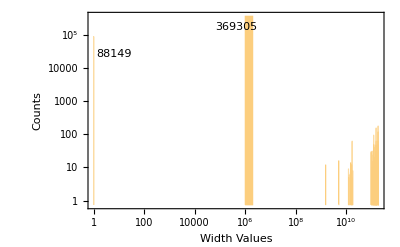

```mathematica
Histogram[datafull[[All,9]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,ChartLabels->Placed[{88149,369305},{{0.07,0.8},Top},Framed[#,FrameMargins->1,Background->LightYellow]&],FrameLabel->{"Width Values","Counts"}]
```

```mathematica
widthmodified=Table[If[StringQ@i,i,If[(RealDigits@i)[[2]]>4,i/10^((RealDigits@i)[[2]]-4),i,i]],{i,datafull[[All,9]]}]
Counts@(Head/@widthmodified)
```

{1240.,1240.,1240.,1240.,1240.,1240.,1240.,1230.,1230.,1230.,1230.,1230.,1230.,1230.,1220.,1220.,1220.,1220.,1220.,1220.,1220.,1220.,1230.,1230.,1230.,1230.,1230.,1230.,1230.,1530.,1530.,1530.,1530.,1530.,1530.,1530.,1520.,1520.,1520.,1520.,1520.,1520.,1520.,1520.,0,0,0,0,1240.,1240.,459103,0,0,0,0,0,0,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1350.,1360.,1360.,1360.,1360.,0,0,0,0,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1360.,1350.,1350.,1350.,1350.,NA,NA}
 |  |  |  |

<|Real→397873,Integer→61183,String→147|>

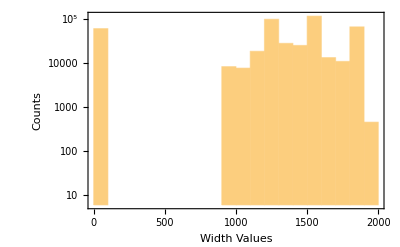

```mathematica
Histogram[widthmodified,ScalingFunctions->"Log",PlotRange->{{0,2000},All},Frame->True,FrameLabel->{"Width Values","Counts"}]
```

Thickness Feature

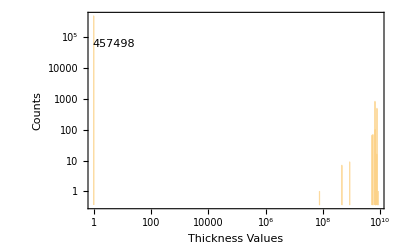

```mathematica
Histogram[datafull[[All,10]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,ChartLabels->Placed[457498,{0.07,0.85},Framed[#,FrameMargins->1,Background->LightYellow]&],FrameLabel->{"Thickness Values","Counts"}]
```

```mathematica
thicknessmodified=Table[If[StringQ@i,i,If[(RealDigits@i)[[2]]>2,i/10^((RealDigits@i)[[2]]-2),i,i]],{i,datafull[[All,10]]}]
Counts@(Head/@thicknessmodified)
```

{87.,87.,87.,87.,87.,87.,87.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,65.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,66.,0,0,0,0,67.,67.,67.,67.,67.,67.,65.,65.,65.,65.,65.,65.,65.,65.,0,0,0,0,0,0,0,65.,459063,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,0,0,0,0,0,0,67.,67.,67.,67.,67.,67.,66.,66.,66.,66.,66.,66.,67.,67.,67.,67.,0,0,0,0,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,67.,NA,NA}
 |  |  |  |

<|Real→397860,Integer→61199,String→144|>

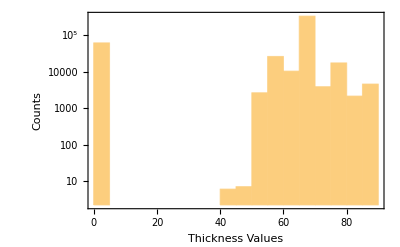

```mathematica
Histogram[thicknessmodified,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"}]
```

Time Windows Generation by Data Partitioning

```mathematica
datafull[[All,9]]=widthmodified;
datafull[[All,10]]=thicknessmodified;
data=Table[Take[datafull,UpTo@i],{i,Ceiling@Range[45920.3,459203,45920.3]}];
```

Investigation for Constraints Impact in Time Windows

Networks with Nodes in Fixed Step Size

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,20,10];]
```

{576.821,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

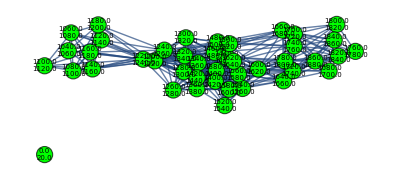
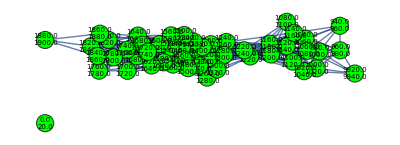
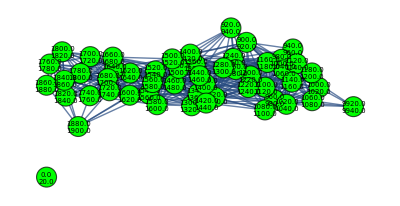
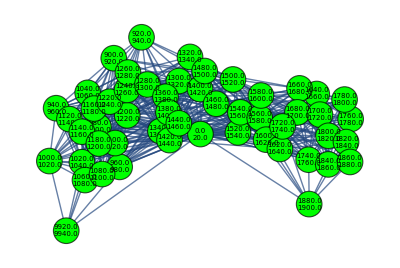
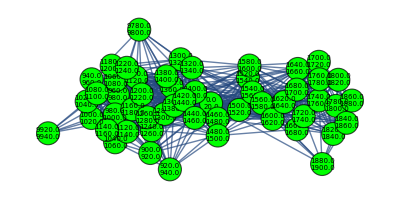
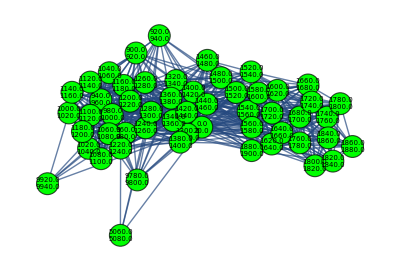
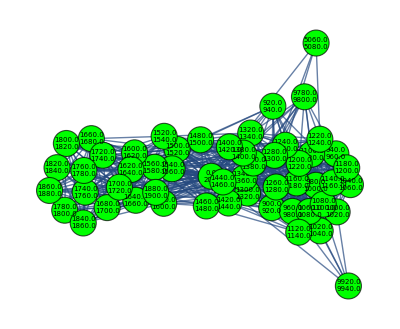
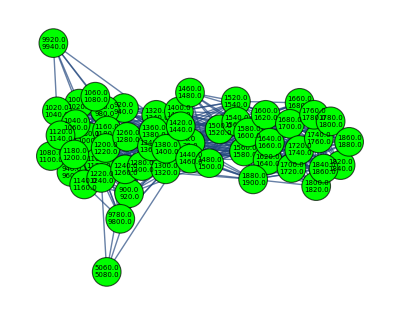
{{-Graphics-,43},{-Graphics-,50},{-Graphics-,52},{-Graphics-,52},{-Graphics-,53},{-Graphics-,54},{-Graphics-,54},{-Graphics-,54},{-Graphics-,54},{-Graphics-,55}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.82685,-0.802254},{0.727488,-0.818188},{0.916597,-0.844139},{0.958415,-0.991312},{0.904981,-0.977276},{0.94656,-0.920367},{0.913365,-0.972152},{0.909537,-0.932581},{0.905554,-0.981126},{0.839404,-0.81029}}

{{0.631156,-0.498935},{0.582659,-0.430381},{0.758536,-0.467369},{0.698999,-0.599264},{0.647809,-0.601992},{0.660276,-0.602837},{0.643621,-0.592007},{0.650955,-0.570753},{0.645284,-0.574911},{0.596069,-0.494557}}

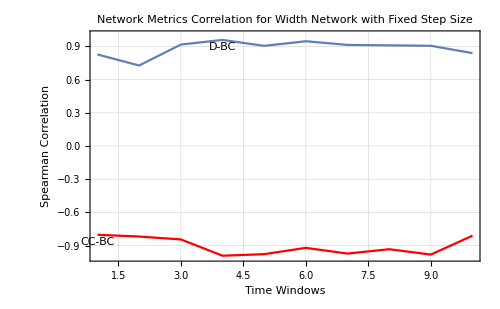
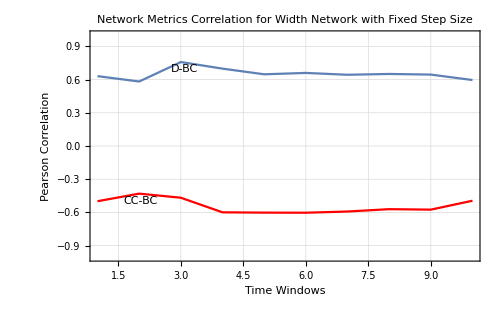

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-4.78392},{2,-12.0224},{3,-1.91662},{4,0.503168},{5,-3.0229},{6,-0.448509},{7,-3.00929},{8,-3.00743},{9,-3.38189},{10,-7.74058}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.00391},{2,-3.65197},{3,-3.48071},{4,-4.31706},{5,-4.34677},{6,-3.93391},{7,-4.30261},{8,-4.01452},{9,-4.26258},{10,-3.36863}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-16.5366},{2,-22.714},{3,-14.2497},{4,-21.5248},{5,-25.8088},{6,-26.5365},{7,-29.7302},{8,-27.3755},{9,-28.0418},{10,-31.3332}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-1.1971},{2,-1.06497},{3,-1.05133},{4,-1.79644},{5,-1.86207},{6,-1.87206},{7,-1.79809},{8,-1.65366},{9,-1.58714},{10,-1.28099}}

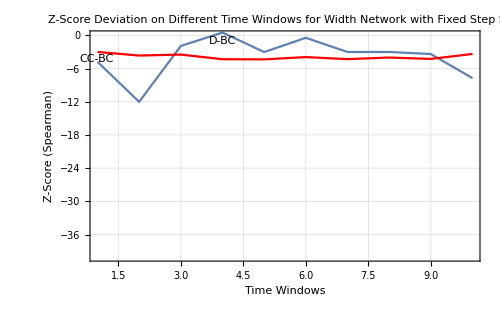
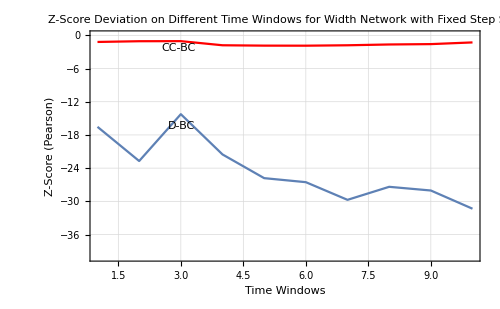

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.1,10];]
```

{3536.24,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

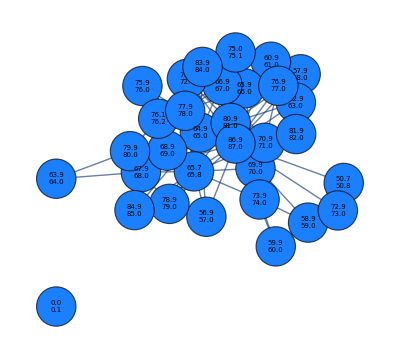
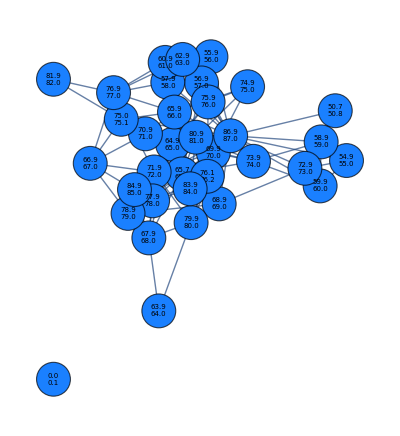
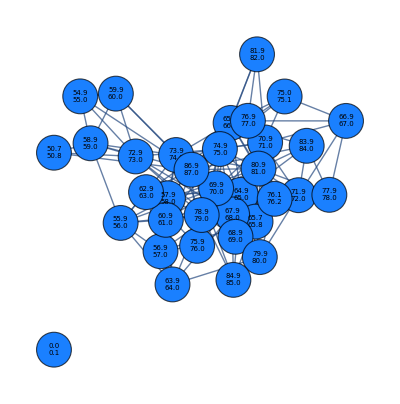
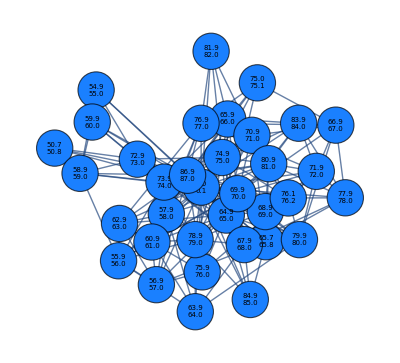
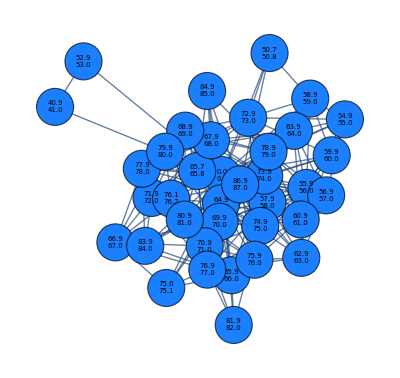
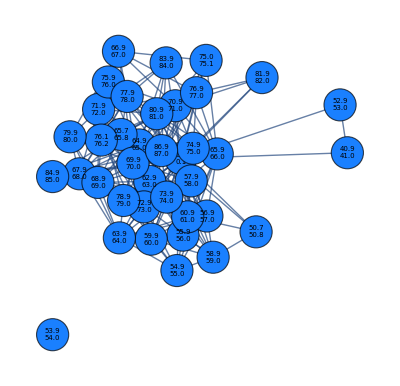
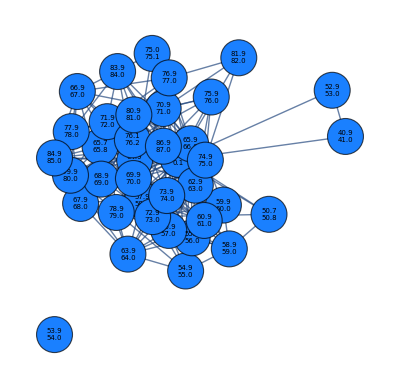
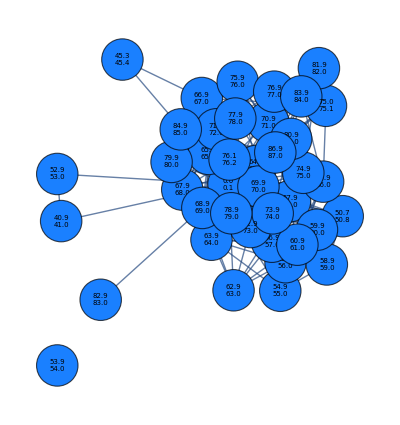
{{-Graphics-,32},{-Graphics-,35},{-Graphics-,35},{-Graphics-,35},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,40},{-Graphics-,41},{-Graphics-,41}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.932783,-0.796727},{0.908849,-0.716695},{0.916719,-0.7004},{0.93912,-0.906811},{0.95285,-0.889666},{0.935017,-0.722435},{0.939483,-0.699436},{0.943043,-0.53645},{0.927237,-0.686511},{0.94354,-0.25778}}

{{0.869248,-0.46858},{0.843132,-0.421728},{0.770286,-0.472945},{0.877292,-0.518271},{0.809918,-0.446188},{0.768257,-0.334724},{0.752032,-0.330238},{0.723693,-0.22225},{0.746908,-0.275495},{0.663251,-0.0583977}}

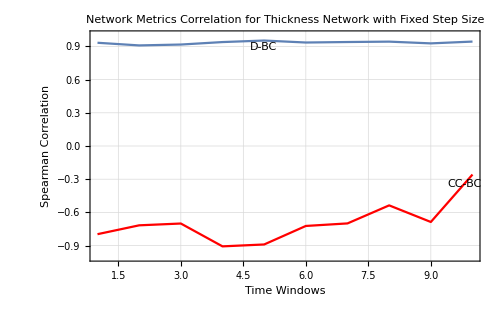
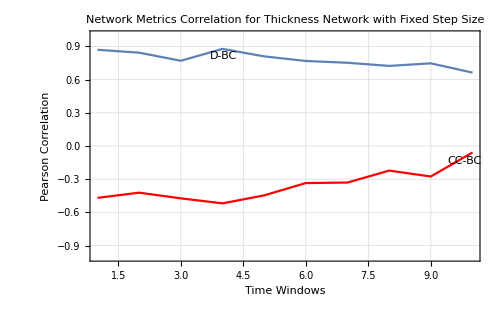

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,0.513603},{2,-0.258377},{3,-0.104282},{4,0.565508},{5,1.07189},{6,0.367045},{7,0.478779},{8,0.559077},{9,-0.0694945},{10,0.590463}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.10859},{2,-2.73123},{3,-2.40751},{4,-3.46177},{5,-3.3986},{6,-2.49543},{7,-2.42854},{8,-1.50394},{9,-2.47674},{10,0.109912}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.576023},{2,-1.64904},{3,-4.13987},{4,-1.43423},{5,-4.2623},{6,-5.6921},{7,-6.62055},{8,-8.47877},{9,-7.56998},{10,-9.23535}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-1.68135},{2,-1.34421},{3,-1.32984},{4,-1.33201},{5,-0.9891},{6,-0.2925},{7,-0.278031},{8,0.356254},{9,0.0282377},{10,1.29413}}

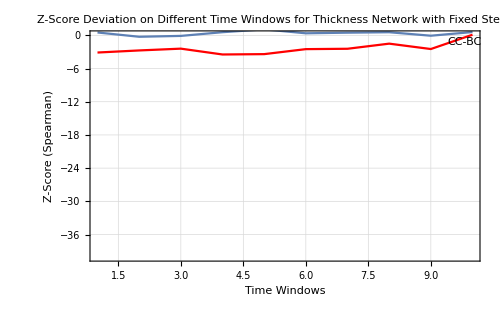
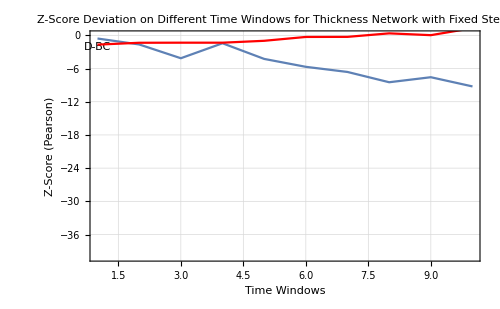

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"]}
```